```mathematica
ClearAll[MW,d1,T1,P2,Cp,ρ,sol];
```

```mathematica
Manipulate[
Module[{MW,d1,T1,P2,Cp,ρ,sol,ρ2},
MW=0.02897;(*kg/mol*)

d1=0.06;(*m*)
T1=400;(*K*)
P2=101.3;

Cp=5/2*8.314/MW;(*J/kg/K*)
(*ρ[T_]:=Quiet@Interpolation[{#,P2/(8.314*^-3/MW*#)}&/@Range[100,400]][T];*)
ρ[T_]:=P2/(8.314*^-3/MW*T);

(*sol=Quiet@Solve[Cp*(t-T1)==1/2*(u1^2-u^2)∧u1*d1^2*P2/T1==u*d2^2*P2/t,{t,u},Reals];*)
sol=Quiet@Solve[Cp*(t-T1)==1/2*(u1^2-u^2)∧u1*d1^2*ρ[T1]==u*d2^2*ρ[t],{t,u},Reals];
sol
(*ρ2[T_]:=Evaluate[Fit[{#,P2/(8.314*^-3/MW*#)}&/@Range[100,400],{1,x,x^2,x^3(*,x^4*)},x]]/.x->T;

Plot[{ρ[T],ρ2[T]},{T,100,600},PlotStyle->{{Thick,Red},{Thick,Dashed,Black}},ImageSize->450]*)

],
Control[{{u1,100,"inlet velocity (m/s)"},10,150,1,Appearance->"Labeled"}],
Control[{{d2,0.03,"outlet diameter (m)"},0.02,0.1,0.01,Appearance->"Labeled"}]
]
```

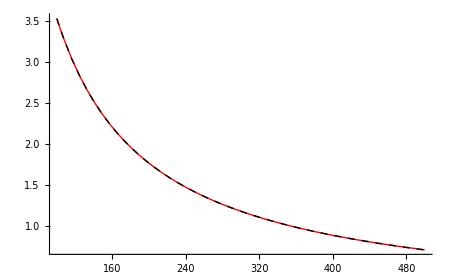

```mathematica
Module[{P2,MW,ρ},
P2=101.3;(*kPa*)
MW=0.02897;(*kg/mol*)
ρ[T_]:=P2/(8.314*^-3/MW*T);

Show[
Plot[ρ[T],{T,100,500},PlotStyle->{Thick,Red}],
Plot[Quiet@Interpolation[{#,ρ[#]}&/@Range[100,400]][T],{T,100,500},PlotStyle->{Thick,Dashed,Black}],
ImageSize->450]
]
```